```mathematica
h=6.626*^-34;(*J*s*)
c=299792458*^6;(*μm/s*)
kB=1.3806*^-23;(*J/K*)
nA=6.022*^23;
```

```mathematica
am15=Import["C:\\Users\\eschl\\Dropbox (MIT)\\MIT\\_Grad\\MADMEC 2022\\Insolation\\AM0AM1_5.xls"];
am15direct=Map[{1/1000.,1}*#&,am15[[3,3;;,{1,4}]]];
am15global=Map[{1/1000.,1}*#&,am15[[3,3;;,{1,3}]]];
```

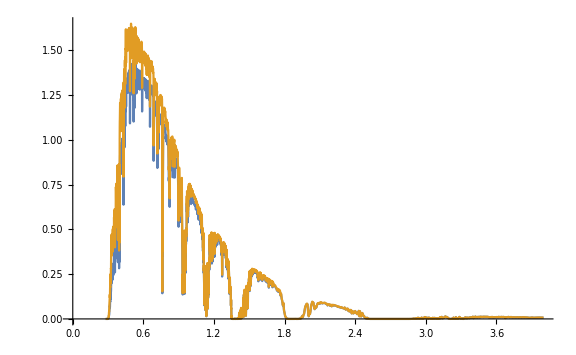

```mathematica
ListLinePlot[{am15direct,am15global},ImageSize->Large]
```

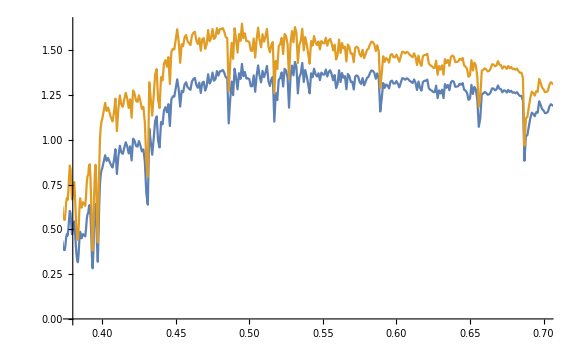

```mathematica
ListLinePlot[{am15direct,am15global},PlotRange->{{0.380,0.700},Automatic},ImageSize->Large]
```

```mathematica
am15directF:=Interpolation[am15direct,InterpolationOrder->1]
am15globalF:=Interpolation[am15global,InterpolationOrder->1]
```

```mathematica
NIntegrate[am15globalF[λ],{λ,0.28,4}]//Quiet
```

1.00477

```mathematica
NIntegrate[am15globalF[λ],{λ,0.28,0.30}]//Quiet
```

1.48391×10^-6

```mathematica
(*Photosynthetic photon flux density in max direct sun*)
1120/(h c nA)NIntegrate[λ*am15globalF[λ],{λ,0.4,0.7}]//Quiet
```

0.00221529

```mathematica
atmTransmittanceNIR=Import["C:\\Users\\eschl\\Dropbox (MIT)\\MIT\\_Grad\\MADMEC 2022\\Insolation\\cptrans_zm_23_15.txt","Data"];
```

```mathematica
atmTransmittanceMIR=Import["C:\\Users\\eschl\\Dropbox (MIT)\\MIT\\_Grad\\MADMEC 2022\\Insolation\\cptrans_nq_23_15.txt","Data"];
```

```mathematica
Show[ListLinePlot[{atmTransmittanceNIR,atmTransmittanceMIR},PlotRange->All,ImageSize->Large],Plot[10^11 planck[λ,300],{λ,0,25},PlotStyle->Black]]
```

-Graphics-

```mathematica
planck[λ_,T_]:=(2h c^2)/λ^5 1/(Exp[h c/(λ kB T)]-1)
```

General::munfl: 3.42794×10^12 2.947218072×10^-44818 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.42794×10^12 1.114718393×10^-40784 is too small to represent as a normalized machine number; precision may be lost.

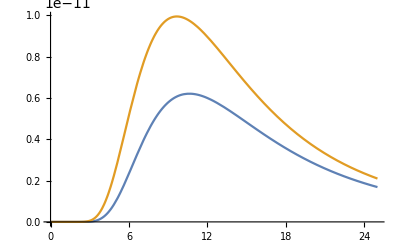

```mathematica
Plot[{planck[λ,273],planck[λ,300]},{λ,0,25}]
```

```mathematica
relativeAction=Transpose[{Range[0.350,0.750,0.025],{0.09,0.28,0.43,0.52,0.54,0.51,0.56,0.55,0.61,0.75,0.88,0.95,0.96,1.00,0.42,0.09,0.02}}]
relativeActionF=Interpolation[relativeAction,InterpolationOrder->3,Method->"Spline"]
```

{{0.35,0.09},{0.375,0.28},{0.4,0.43},{0.425,0.52},{0.45,0.54},{0.475,0.51},{0.5,0.56},{0.525,0.55},{0.55,0.61},{0.575,0.75},{0.6,0.88},{0.625,0.95},{0.65,0.96},{0.675,1.},{0.7,0.42},{0.725,0.09},{0.75,0.02}}

InterpolatingFunction[…]

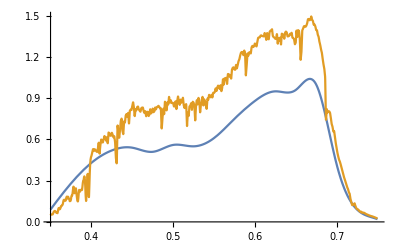

```mathematica
Plot[{relativeActionF[λ],relativeActionF[λ]*am15globalF[λ]},{λ,.350,.750}]
```